# 函数

## 对数刻度

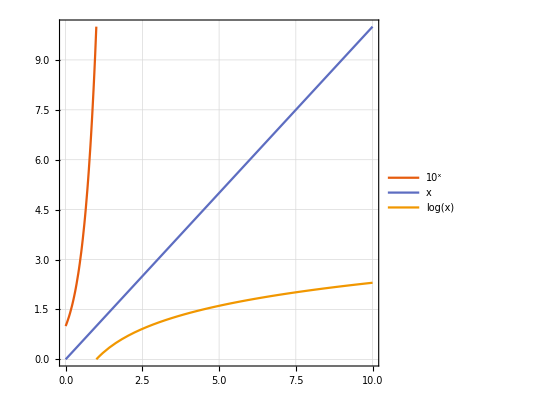
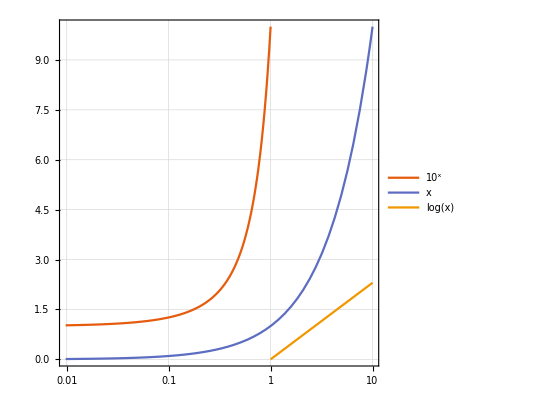
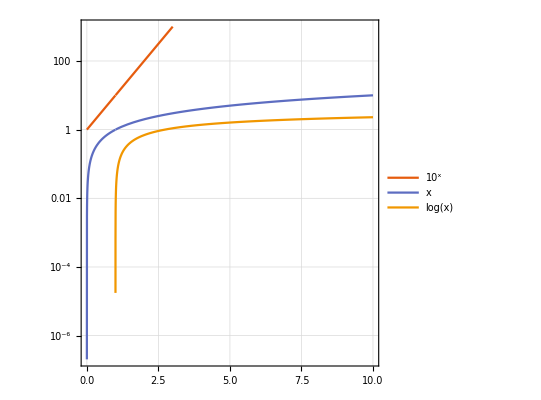
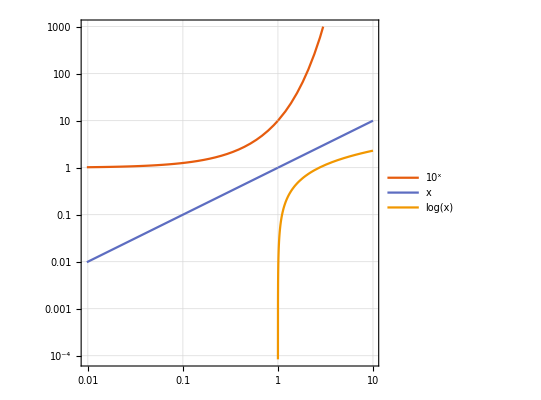

```mathematica
#[[1]][{10^x,x,Log[x]},{x,0,10},PlotRange->{0,#[[2]]},PlotTheme->"Scientific",PlotLegends->"Expressions",AspectRatio->1/1,GridLines->Automatic]&/@{{Plot,10},{LogLinearPlot,10},{LogPlot,1000},{LogLogPlot,1000}}(*对数刻度和线性刻度在横纵轴的搭配*)
```

## 累计求和

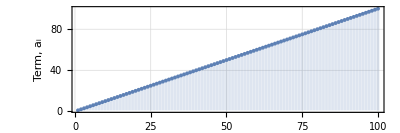

```mathematica
DiscretePlot[k,{k,1,100},PlotRange->All,PlotMarkers->{Automatic, Tiny},AspectRatio->1/3,GridLines->Automatic,Frame->True,FrameLabel->{"Index, k","Term, a_i"}]
```

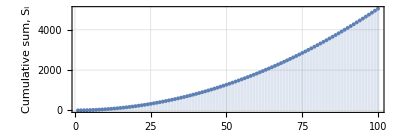

```mathematica
Accumulate@Range[100];
DiscretePlot[%[[k]],{k,1,100},PlotRange->All,PlotMarkers->{Automatic, Tiny},AspectRatio->1/3,GridLines->Automatic,Frame->True,FrameLabel->{"Index, k","Cumulative sum, S_i"}]
```

## 数列极限估算圆周率

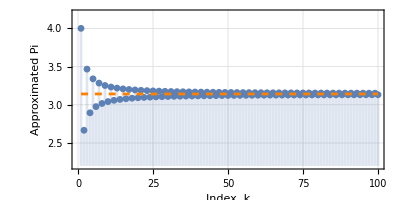

```mathematica
4Sum[(-1)^(k+1)/(2k-1),{k,1,n}];
Show[DiscretePlot[%,{n,1,100},PlotRange->{2.2,4.2},AspectRatio->1/2,PlotMarkers->{Automatic,Small},GridLines->Automatic,Frame->True,FrameLabel->{"Index, k","Approximated Pi"}],Plot[Pi,{x,1,100},PlotStyle->{Orange,Dashed}]]
```